# Bessel Functions

## Bessel equation and Bessel functions

### Bessel functions arise in solving differential equations for systems in cylindrical coordinates. J_n(z) is often called the Bessel function of the first kind, or simply the Bessel function. Y_n(z) is referred to as the Bessel function of the second kind. ◼ BesselJ[n, z] gives the Bessel function of the first kind, J_n(z). ◼ BesselY[n, z] gives the Bessel function of the second kind, Y_n(z). The Bessel functions J_n(z) and Y_n(z) are linearly independent solutions to the Bessel equation z^2(ϕ̄)_n''+z(ϕ̄)_n'+(z^2-n^2)(ϕ̄)_n=0. That is, for integer n, (ϕ̄)_n(z) = A_n*J_n(z) + B_n*Y_n(z).

## Properties of Bessel functions ⇒ Plots ⇒ Behavior at z=0.

### Bessel function of the first kind.

#### For integer n, the J_n(z) are regular at z=0. At z=0, J_0(0)=1 and J_n(0)=0, for n=1, 2, 3, ...

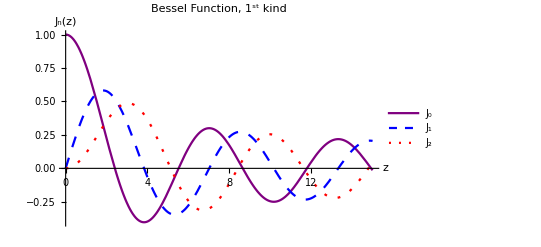

```mathematica
Plot[{BesselJ[0,z],BesselJ[1,z],BesselJ[2,z]},{z,0,15},PlotLabel->"Bessel Function, 1^st kind",AxesLabel->{"z","J_n(z)"},PlotStyle->{Directive[Purple,Thick],Directive[Thick,Blue,Dashing[{0.02,0.02}]],Directive[Thick,Red,Dashing[{0.005,0.02}]]},PlotLegends->{"J_0","J_1","J_2"},BaseStyle->{FontSize->14}]
```

### Bessel function of the second kind.

#### For integer n, the Y_n(z) have a logarithmic divergence at z=0. ⇒ For problems that contain z=0 in their domain, with a finiteness condition lim_(z→0) |(ϕ̄)_n(z)|<∞, the coefficient of the Y_n(z) terms must equal zero.

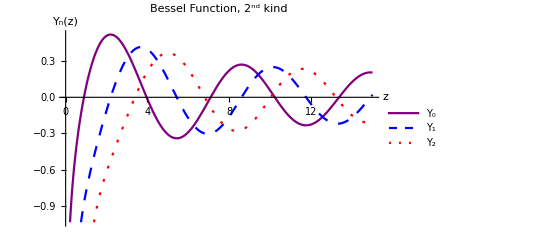

```mathematica
Plot[{BesselY[0,z],BesselY[1,z],BesselY[2,z]},{z,0,15},PlotLabel->"Bessel Function, 2^nd kind",AxesLabel->{"z","Y_n(z)"},PlotStyle->{Directive[Purple,Thick],Directive[Thick,Blue,Dashing[{0.02,0.02}]],Directive[Thick,Red,Dashing[{0.005,0.02}]]},PlotLegends->{"Y_0","Y_1","Y_2"},BaseStyle->{FontSize->14}]
```

## Properties of Bessel functions ⇒ Oscillatory behavior ⇒ Zeros

### Bessel function of the first kind. All the J_n(z) are oscillatory ⇒ There are an infinite number of solution for J_n(z)=0, yielding an infinite number of eigenfunctions required by the S.L. eigenvalue problem theorem for the disk problem. ⇒ Denote the k^th root of J_n(z) as z_(n k). Therefore, J_n(z_(n k))=0. ⇒ Mathematica has a built-in function to find the roots, z_(n k) = BesselJzero[n,k]. The first few roots are given in the table.

```mathematica
TableForm[Table[{k,N[BesselJZero[0,k]],N[BesselJZero[1,k]]},{k,1,4}],TableHeadings->{{},{"k","z_(0  k)","z_(1  k)"}}]
```

| k | z_(0  k) | z_(1  k)
 | 1 | 2.40483 | 3.83171
 | 2 | 5.52008 | 7.01559
 | 3 | 8.65373 | 10.1735
 | 4 | 11.7915 | 13.3237

### Bessel function of the second kind. All the Y_n(z) are oscillatory ⇒ There are an infinite number of solution for Y_n(z)=0. ⇒ Denote the k^th root of Y_n(z) as s_(n k). Therefore, Y_n(s_(n k))=0. ⇒ Mathematica has a built-in function to find the roots, s_(n k)= BesselYzero[n,k]. The first few roots are given in the table.

```mathematica
TableForm[Table[{k,N[BesselYZero[0,k]],N[BesselYZero[1,k]]},{k,1,4}],TableHeadings->{{},{"k","s_(0  k)","s_(1  k)"}}]
```

| k | s_(0  k) | s_(1  k)
 | 1 | 0.893577 | 2.19714
 | 2 | 3.95768 | 5.42968
 | 3 | 7.08605 | 8.59601
 | 4 | 10.2223 | 11.7492

## Properties of Bessel functions ⇒ Expressions in terms of infinite series ⇒ Asymptotic forms

### Infinite series expressions for J_n(z) and Y_n(z) , if n is an integer. J_n(z)∼∑_(k=0)^∞ (-1)^k/(k!(n+k)!)(x/2)^(2k+n) Y_n(z)∼lim_(ν→n) (J_ν(x)Cos(νπ)-J_-ν(x))/(Sin(νπ)), with J_ν(z)∼∑_(k=0)^∞ (-1)^k/(k!Γ(ν+k+1))(x/2)^(2k+n), when ν is not an integer, where Γ is the Gamma function.

### Asymptotic forms for J_n(z) and Y_n(z) for large z ⇒ For large z, the roots are separated by π. That is, z_(n k+1) - z_(n k) → π, as k becomes large. J_n(z)∼√(2/(π z))Cos[z - π/4 -(n π)/2] Y_n(z)∼√(2/(π z))Sin[z - π/4 -(n π)/2]

### Asymptotic form or J_n(z) and Y_n(z) for small z ⇒ For small z, J_0(0)=1 and J_n(0)=0 for n>0. J_n(z)∼{1, n=0 1/(2^n n!)z^n, n>0. ⇒ For small z, Y_n(0) is infinite. Therefore, it cannot satisfy the finiteness condition at r=0. Y_n(z)∼{2/π ln(z), n=0 (-2^n(n-1)!)/π z^-n , n>0.

## Properties of Bessel functions ⇒ ORTHOGONALITY

#### The orthogonality+ statement for a circular membrane (from the Sturm-Liouville Theorem) is ∫_0^a rϕ_(m p)ϕ_(m q)ⅆr=∫_0^a r J_m(z_(m p)r/a)J_m(z_(m q)r/a)ⅆr=0, p≠q. The integral ∫_0^a r (J_m(z_(m p)r/a))^2 ⅆr = (a^2/2[J'_m(z_mp)])^2=(a^2/2[J_(m+1)(z_mp)])^2. The mode shapes for the complete circular membrane involved only the Bessel function of the first kind. Both Bessel functions of the first and second kind are involved for annular membranes.

A few checks on the statement of ORTHOGANALITY.  Show that ∫_0^a rϕ_(0,1)ϕ_(0,3)ⅆr=0, ∫_0^a rϕ_(0,1)ϕ_(0,1)ⅆr  =(a^2/2[J'_0(z_(0,1))])^2

```mathematica
z01=N[BesselJZero[0,1]];z03=N[BesselJZero[0,3]];
```

```mathematica
∫_0^a r*BesselJ[0,z01*r/a]*BesselJ[0,z03*r/a]ⅆr
```

0.

```mathematica
Chop[∫_0^a r*BesselJ[0,z01*r/a]*BesselJ[0,z01*r/a]ⅆr]
```

0.134757 a^2

```mathematica
DBesselJ[m_,z_]=D[BesselJ[m,z],z];
a^2/2*(DBesselJ[0,z01])^2
```

0.134757 a^2

#### The derivative of J'_m(z)=1/2(J_(m-1)(z)-J_(m+1)(z))

```mathematica
DBesselJm[m_,z_]=D[BesselJ[m,z], z]
```

1/2 (BesselJ[-1+m,z]-BesselJ[1+m,z])